# Quantum Methods With Mathematica

基本波动力学

### 定义哈密顿算符

```mathematica
hamilton[V0_]@psi_:=-h^2/(2m) D[psi,{x,2}]+V0 psi
```

```mathematica
hamilton[V0][Exp[I k x]]//Collect[#,Exp[I k x]]&
```

ⅇ^(ⅈ k x) ((h^2 k^2)/(2 m)+V0)

### 定义动量算符

```mathematica
p[l_]:=-I h D[l,x]
```

### 定义薛定谔算符

```mathematica
schroedingerD[V_][psi_]:=hamilton[V][psi]-Energy psi
```

尝试

```mathematica
schroedingerD[V[x]][psi[x]]==0
```

-Energy psi[x]+psi[x] V[x]-(h^2 psi''[x])/(2 m)==0

### 时变算符

盒子中的粒子

```mathematica
phi[n_,x_]:=norm[n] Sin[n Pi x/L]
```

```mathematica
schroedingerD[0][phi[n,x]]/phi[n,x]==0//ExpandAll
```

-Energy+(h^2 n^2 π^2)/(2 L^2 m)==0

```mathematica
e[n_]=Energy/.Solve[%,Energy][[1]]
```

(h^2 n^2 π^2)/(2 L^2 m)

```mathematica
NDSolve[{schroedingerD[0][phi[x]]==0,phi[0]==0,phi'[0]==1}/.{h->1,m->1,Energy->4.0},phi,{x,0,1.1}]
```

{{phi→InterpolatingFunction[…]}}

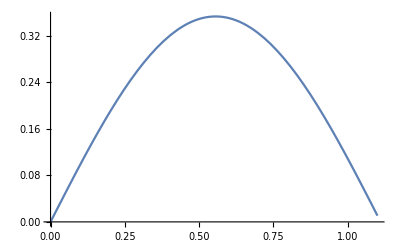

```mathematica
Plot[phi[x]/.%,{x,0,1.1}]
```

```mathematica
norm[n_]=norm[n]/.Solve[Integrate[phi[n,x]^2,{x,0,L}]==1/.Sin[m_Integer n Pi]->0,norm[n]][[1]]
```

-(√2)/(√L)

### 部分和：傅里叶展开

```mathematica
psi[x_][nmax_]:=Sum[c[n] phi[n,x],{n,1,nmax}]
```

```mathematica
psi[x][8]
```

-(√2 c[1] Sin[(π x)/L])/(√L)-(√2 c[2] Sin[(2 π x)/L])/(√L)-(√2 c[3] Sin[(3 π x)/L])/(√L)-(√2 c[4] Sin[(4 π x)/L])/(√L)-(√2 c[5] Sin[(5 π x)/L])/(√L)-(√2 c[6] Sin[(6 π x)/L])/(√L)-(√2 c[7] Sin[(7 π x)/L])/(√L)-(√2 c[8] Sin[(8 π x)/L])/(√L)

```mathematica
c[n_]=Integrate[Sqrt[2/L]phi[n,x],{x,L/4,3L/4}]
```

-(4 √(1/L) √L Sin[(n π)/4] Sin[(n π)/2])/(n π)

### 演示

```mathematica
Table[c[n],{n,14}]/.L->1
```

{-(2 √2)/π,0,(2 √2)/(3 π),0,(2 √2)/(5 π),0,-(2 √2)/(7 π),0,-(2 √2)/(9 π),0,(2 √2)/(11 π),0,(2 √2)/(13 π),0}

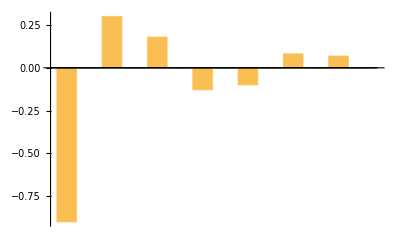

```mathematica
BarChart[Table[c[n],{n,14}]/.{L->1}]
```

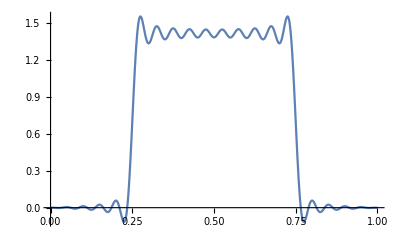

```mathematica
Plot[Table[psi[x][n],{n,40,40}]/.{L->1.},{x,0,1}]
```

不确定性原理

```mathematica
a[n_]:=1/Sqrt[2]
```

```mathematica
a[n_,t_]:=a[n] Exp[-I e[n]t/h]
```

```mathematica
psi[x_,t_]:=Sum[a[n,t] phi[n,x],{n,1,2}]
```

```mathematica
psi[x,t]
```

-(ⅇ^(-(ⅈ h π^2 t)/(2 L^2 m)) Sin[(π x)/L])/(√L)-(ⅇ^(-(2 ⅈ h π^2 t)/(L^2 m)) Sin[(2 π x)/L])/(√L)

# Let Me See You Mother Fuckers Put Them Up In Th Sky!

量子力学中的态的均值和算符均值根本不是一码子事情……

```mathematica
Expect[q_,psi_]:=Integrate[ComplexExpand[q[psi]]*ComplexExpand[Conjugate[psi]],{x,-Infinity,Infinity}]
```

```mathematica
del[q_,psi_]:=Sqrt[Integrate[Abs[q[psi]-Expect[p,psi]]^2,{x,-Infinity,Infinity}]]
```

### 定义坐标算符

```mathematica
X[l_]:=x*l
```

```mathematica
guass[x_]:=(A/Pi)^(1/4)*Exp[-A x^2/2]
```

```mathematica
FourierTransform[guass[x],x,ω]/.{ω->k}
```

(ⅇ^(-k^2/(2 A)))/(A^(1/4) π^(1/4))

```mathematica
Assuming[A>0,Expect[p,guass[x]]]
```

0

```mathematica
Assuming[A>0&&h>0,del[p,guass[x]]]//Simplify
```

(√(A h^2))/(√2)

### Fuck That! It works ! Under this situation: -Graphics-

```mathematica
psi[x,t]
```

-(ⅇ^(-(ⅈ h π^2 t)/(2 L^2 m)) Sin[(π x)/L])/(√L)-(ⅇ^(-(2 ⅈ h π^2 t)/(L^2 m)) Sin[(2 π x)/L])/(√L)